```mathematica
ClearAll["Global`*"]
```

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/test.csv"][[2;;]];
tline=Table[{tline[[i,2]],tline[[i,3]]},{i,2,Length[tline]}]
```

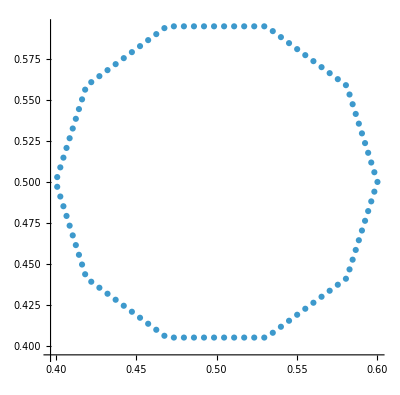

```mathematica
ListPlot[tline,AspectRatio->Automatic]
```